```mathematica
Plot3D[3x - y, {x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{17+2*t-7*s, 29+3*t-11* s, 5*t+13*s}, {t,-1,1},{s,-1,1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{17, 29,0} + t*{2,3,5}+s*{-7,-11,13}, {t,-1,1},{s,-1,1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
s*{0,0,1}+t*{0.2,0.2,2}, {s,-1,3},{t,-1,3},
AxesLabel->{"x","y","z"}, BoxRatios->{3, 3, 2}]
```

-Graphics3D-

****Exercise 1:
Plane equation
P(x)=Ax+By+Cz+D=0,
P(x)=A(x-x0)+B(y-y0)+C(z-z0)=0
If A and B are both equal to 0, we would get Cz+D=0 which could be a valid plane that doesn’t rely on x or y.

parameterized plane equation

k= (p)+ t*(u)+s*(v)
Where t and s are both parameters,
u and v are both vectors ,
and p is a point on the plane
any plane can be parameterized
Ex
3x-2y+8Z=0
we can set x to t and y to s
this gives us 8z=-3t+2t
z=-3t/8+t/4

****exercise 1 end

```mathematica
f[x_,y_] = x^2 + 3 x*y + y^2
surf = Plot3D[f[x,y], {x,0,2},{y,-3,-1}, Mesh->False,AxesLabel->{"x","y","z"},PlotStyle->Opacity[0.5]]
```

x^2+3 x y+y^2

-Graphics3D-

```mathematica
fx[x_,y_]=D[f[x,y],x]
fy[x_,y_]=D[f[x,y],y]

fx[1,-2]
fy[1,-2]
```

2 x+3 y

3 x+2 y

-4

-1

```mathematica
tangentvectorx=Graphics3D[{Thick,Line[{{1,-2,-1},{1,-2,-1}+{1,0,-4}}]}];
tangentvectory=Graphics3D[{Thick,Line[{{1,-2,-1},{1,-2,-1}+{0,1,-1}}]}];
Show[surf,tangentvectorx,tangentvectory]
```

-Graphics3D-

```mathematica
p[s_,t_] = {1,-2,f[1,-2]}+s*{1,0,fx[1,-2]}+t*{0,1,fy[1,-2]}
```

{1+s,-2+t,-1-4 s-t}

```mathematica
surf = Plot3D[f[x,y], {x,0,2},{y,-3,-1}, Mesh->5,AxesLabel->{"x","y","z"},PlotStyle->Red,PlotPoints->50];
tanplane =ParametricPlot3D[p[s,t], {s,-1,1}, {t,-1,1},Mesh->5,PlotStyle->Blue,PlotPoints->50];
Show[surf, tanplane]
```

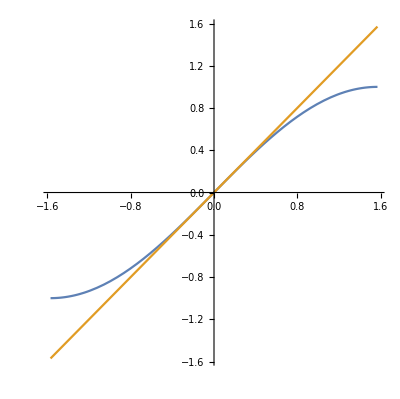
-Graphics- -Graphics3D-

```mathematica
-Graphics3D-Plot[{Sin[x],x},{x,-Pi/2,Pi/2},AspectRatio->Automatic]
```

```mathematica
p[s_,t_] = {1,-2,f[1,-2]}+s*{1,0,fx[1,-2]}+t*{0,1,fy[1,-2]}
```

{1+s,-2+t,-1-4 s-t}

```mathematica
Cross[{1,0,-4},{0,1,-1}]
```

{4,1,1}

```mathematica
surf = Plot3D[f[x,y], {x,0,2},{y,-3,-1}, Mesh->5,AxesLabel->{"x","y","z"},PlotStyle->Red,PlotPoints->50];tanplane2=Plot3D[-4x-y+1,{x,0,2},{y,-1,-3},Mesh->5];
Show[surf,tanplane2]
```

-Graphics3D-

```mathematica
ClearAll
```

ClearAll

****Exercise 2

```mathematica
g(x_,y_)=x^2-y^2
```

x^2-y^2

```mathematica
gx[x_,y_]=D[g[x,y],x]
```

2 x

```mathematica
gy[x_,y_]=D[g[x,y],y]
```

-2 y

```mathematica
gx[1,2]
gy[1,2]
```

2

-4

```mathematica
surf = Plot3D[g[x,y], {x,0,3},{y,0,3},Mesh->5,AxesLabel->{"x","y","z"},PlotStyle->Red,PlotPoints->50]
```

-Graphics3D-

(1,0,g_x(1,2))=(1,0,2)
(0,1,g_y(1,2))=(0,1,-4)

```mathematica
Cross[{1,0,2},{0,1,-4}]
```

{-2,4,1}

parametric equation of the tangent plane 
p[s_,t_] = {1,2,g[1,2]}+s*{1,0,gx[1,2]}+t*{0,1,gy[1,2]}

Normal vector for Cartesian coordinates are {-2,4,1}
Cartesian equation is
-2(x-1)+4(y-2)+(z+3)=0
z=2x-4y+3

```mathematica
p[s_,t_] = {1,2,g[1,2]}+s*{1,0,gx[1,2]}+t*{0,1,gy[1,2]}
```

{1+s,2+t,-3+2 s-4 t}

```mathematica
tanplane1=Plot3D[2x-4*y+3,{x,0,5},{y,0,5},Mesh->5];
```

```mathematica
Show[surf,tanplane1]
```

-Graphics3D-

****exercise 2 finished

```mathematica
f[x_,y_] = x^2 + 3 x*y + y^2
```

x^2+3 x y+y^2

```mathematica
g[x_,y_,z_]=z-f[x,y]
```

-x^2-3 x y-y^2+z

```mathematica
gradg[x_,y_,z_]=Grad[g[x,y,z]]
```

{-2 x-3 y,-3 x-2 y,1}

```mathematica
gradg[1,-2,-1]
```

{4,1,1}

```mathematica
ClearAll
```

ClearAll

***Exercise 5

```mathematica
f[x_,y_]=y*Cos[x]
```

y Cos[x]

```mathematica
g[x_,y_,z_]=z-f[x,y]
```

z-y Cos[x]

```mathematica
gradg[x_,y_,z_]=Grad[g[x,y,z]]
```

{y Sin[x],-Cos[x],1}

```mathematica
gradg[0,Pi/4,f[0,Pi/4]]
```

{0,-1,1}

```mathematica
f[0,Pi/4]
```

π/4

Cartesian equation of tangent plane at (0,π/4,f(0,π/4)) is
0(x-0)-1(y-π/4)+(z-f(0,π/4))=0
z=y-π/4+f(0,π/4) ->z=y-π/4+π/4->z=y

```mathematica
surf = Plot3D[f[x,y], {x,-Pi,Pi},{y,-Pi,Pi}, Mesh->5,AxesLabel->{"x","y","z"},PlotStyle->Red,PlotPoints->50]
```

-Graphics3D-

```mathematica
tanpln= Plot3D[z=y+0*x,{x,-Pi,Pi},{y,-Pi,Pi}]
```

```mathematica
Show[tanpln,surf]
```

-Graphics3D-

Exercise 5 finsished